```mathematica
f[x_,y_]=Subscript[r, 1] x(1-x/Subscript[k, 1])-Subscript[α, 1] x y;
g[x_,y_]=Subscript[r, 2] y(1-y/Subscript[k, 2])-Subscript[α, 2] x y;
w[x_,y_]=f[x,y]+g[x,y];
```

```mathematica
{Subscript[r, 1],Subscript[r, 2]}={0.05,0.08};
{Subscript[k, 1],Subscript[k, 2]}={1.5 10^5, 4 10^5};
{Subscript[α, 1],Subscript[α, 2]}={10^-8,10^-8};
```

```mathematica
sols = Solve[Grad[w[x,y],{x,y}]=={0,0},{x,y}]
w[sols[[1,1,2]],sols[[1,2,2]]]
f[sols[[1,1,2]],sols[[1,2,2]]]
g[sols[[1,1,2]],sols[[1,2,2]]]
```

{{x→69103.7,y→196545.}}

9589.38

1727.59

7861.79

```mathematica
sols[[1,2,2]]
```

196545.

```mathematica
Plot3D[w[x,y],{x,-300000,300000},{y,-300000,300000}]
```

-Graphics3D-

```mathematica
NSolve[w[x,y]==0,{x,y}]
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with 151145\ x/110742 - 17791\ y/18457 == 1.

{{x→214096.,y→303144.},{x→0.508315,y→-0.317696}}

```mathematica
NSolve[f[x,y]==0,{x,y}]
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -17791\ x/18457 + 151145\ y/110742 == 1.

{{x→146888.,y→103740.},{x→0.,y→0.732687}}

```mathematica
Plot3D[f[x,y],{x,-300000,300000},{y,-300000,300000}]
```

-Graphics3D-

```mathematica
inequal1[x_,y_]=((Subscript[r, 1]-Subscript[α, 1] y)Subscript[k, 1])/Subscript[r, 1]-x;
inequal2[x_,y_]=((Subscript[r, 2]-Subscript[α, 2] x)Subscript[k, 2])/Subscript[r, 2]-y;
```

```mathematica
RegionPlot3D[inequal1[x,y] ≥ 0 &&inequal2[x,y]≥0,{x,-300000,300000},{y,-300000,300000}]
```

RegionPlot3D::pllim: Range specification Lighting → Automatic is not of the form {x, xmin, xmax}.

General::stop: Further output of RegionPlot3D :: pllim will be suppressed during this calculation.

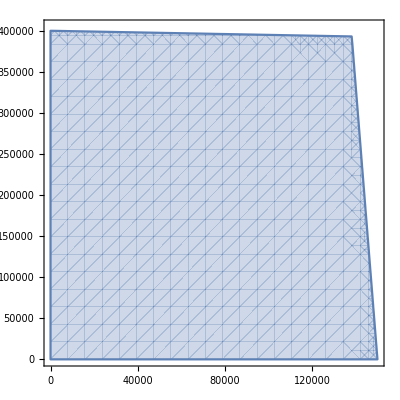

```mathematica
RegionPlot[inequal1[x,y]≥0&&inequal2[x,y]≥0,{x,0,150000},{y,0,405000}]
```

```mathematica
Reduce[inequal1[x,y]≥0&&inequal2[x,y]≥0&&Subscript[r, 1]<Subscript[k, 1]&&Subscript[r, 1]<Subscript[k, 2]&&Subscript[r, 2]<Subscript[k, 1]&&Subscript[r, 2]<Subscript[k, 2]&&Subscript[α, 1]<Subscript[r, 1]&&Subscript[α, 1]<Subscript[r, 2]&&Subscript[α, 2]<Subscript[r, 1]&&Subscript[α, 2]<Subscript[r, 2]&&Subscript[r, 1]>0&&Subscript[r, 2]>0&&Subscript[k, 1]>0&&Subscript[k, 2]>0&&Subscript[α, 1]>0&&Subscript[α, 2]>0≥0&&x>0&&y>0,{x,y}]
```

(0<r_2<1&&((0<r_1<r_2&&0<α_2<r_1&&0<α_1<r_1&&((r_2<k_2<r_1/α_1&&((r_2<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_2<k_1<r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_2<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(r_1==r_2&&0<α_2<r_2&&0<α_1<r_2&&((r_2<k_2<r_1/α_1&&((r_2<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_2<k_1<r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_2<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(r_2<r_1<1&&0<α_2<r_2&&0<α_1<r_2&&((r_1<k_2<r_1/α_1&&((r_1<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_1<k_1<r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(r_1==1&&((0<α_2<r_2^2&&0<α_1<r_2&&((1<k_2<1/α_1&&((1<k_1<r_2/α_2&&((0<x≤(k_1 r_2-k_1 k_2 r_2 α_1)/(r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_2-k_1 k_2 r_2 α_1)/(r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x+k_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==1/α_1&&((1<k_1<r_2/α_2&&0<x<k_1&&0<y≤(-x+k_1)/(k_1 α_1))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>1/α_1&&((1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x+k_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_2-k_1 k_2 r_2 α_1)/(r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x+k_1)/(k_1 α_1))||((k_1 r_2-k_1 k_2 r_2 α_1)/(r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(α_2==r_2^2&&0<α_1<r_2&&((1<k_2<1/α_1&&((1<k_1<r_2/α_2&&((0<x≤(k_1 r_2-k_1 k_2 r_2 α_1)/(r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_2-k_1 k_2 r_2 α_1)/(r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x+k_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==1/α_1&&((1<k_1<r_2/(k_2 α_1 α_2)&&0<x<k_1&&0<y≤(-x+k_1)/(k_1 α_1))||(k_1==r_2/(k_2 α_1 α_2)&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/(k_2 α_1 α_2)&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>1/α_1&&((1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x+k_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_2-k_1 k_2 r_2 α_1)/(r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x+k_1)/(k_1 α_1))||((k_1 r_2-k_1 k_2 r_2 α_1)/(r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(r_2^2<α_2<r_2&&0<α_1<r_2&&((1<k_2<1/α_1&&((1<k_1<r_2/α_2&&((0<x≤(k_1 r_2-k_1 k_2 r_2 α_1)/(r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_2-k_1 k_2 r_2 α_1)/(r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x+k_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==1/α_1&&((1<k_1<r_2/α_2&&0<x<k_1&&0<y≤(-x+k_1)/(k_1 α_1))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>1/α_1&&((1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x+k_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_2-k_1 k_2 r_2 α_1)/(r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x+k_1)/(k_1 α_1))||((k_1 r_2-k_1 k_2 r_2 α_1)/(r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))))||(1<r_1<1/r_2&&((0<α_2≤r_2/r_1^2&&0<α_1<r_2&&((r_1<k_2<r_1/α_1&&((r_1<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_1<k_1<r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(r_2/r_1^2<α_2<r_2/r_1&&0<α_1<r_2&&((r_1<k_2<r_1/α_1&&((r_1<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_1<k_1<(r_1 r_2)/(k_2 α_1 α_2)&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==(r_1 r_2)/(k_2 α_1 α_2)&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>(r_1 r_2)/(k_2 α_1 α_2)&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(r_2/r_1≤α_2<r_2&&0<α_1<r_2&&((r_1<k_2≤r_1/α_1&&k_1>r_1&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_2>r_1/α_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(r_1==1/r_2&&((0<α_2<r_2/r_1^2&&0<α_1<r_2&&((r_1<k_2<r_1/α_1&&((r_1<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_1<k_1<r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(α_2==r_2/r_1^2&&0<α_1<r_2&&((r_1<k_2<r_1/α_1&&((r_1<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_1<k_1<(r_1 r_2)/(k_2 α_1 α_2)&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==(r_1 r_2)/(k_2 α_1 α_2)&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>(r_1 r_2)/(k_2 α_1 α_2)&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(r_2/r_1^2<α_2<r_2/r_1&&0<α_1<r_2&&((r_1<k_2<r_1/α_1&&((r_1<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_1<k_1<r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(r_2/r_1≤α_2<r_2&&0<α_1<r_2&&((r_1<k_2≤r_1/α_1&&k_1>r_1&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_2>r_1/α_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(r_1>1/r_2&&((0<α_2≤r_2/r_1^2&&0<α_1<r_2&&((r_1<k_2<r_1/α_1&&((r_1<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_1<k_1<r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(r_2/r_1^2<α_2<r_2/r_1&&0<α_1<r_2&&((r_1<k_2<r_1/α_1&&((r_1<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_1<k_1<(r_1 r_2)/(k_2 α_1 α_2)&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==(r_1 r_2)/(k_2 α_1 α_2)&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>(r_1 r_2)/(k_2 α_1 α_2)&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(r_2/r_1≤α_2<r_2&&0<α_1<r_2&&((r_1<k_2≤r_1/α_1&&k_1>r_1&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_2>r_1/α_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))))||(r_2==1&&((0<r_1<1&&0<α_2<r_1&&0<α_1<r_1&&((1<k_2<r_1/α_1&&((1<k_1<1/α_2&&((0<x≤(k_1 r_1-k_1 k_2 α_1)/(r_1-k_1 k_2 α_1 α_2)&&0<y≤k_2-x k_2 α_2)||((k_1 r_1-k_1 k_2 α_1)/(r_1-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==1/α_2&&0<x<k_1&&0<y≤k_2-x k_2 α_2)||(k_1>1/α_2&&0<x<1/α_2&&0<y≤k_2-x k_2 α_2)))||(k_2==r_1/α_1&&((1<k_1<1/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==1/α_2&&0<x<k_1&&0<y≤k_2-x k_2 α_2)||(k_1>1/α_2&&0<x<1/α_2&&0<y≤k_2-x k_2 α_2)))||(k_2>r_1/α_1&&((1<k_1≤1/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>1/α_2&&((0<x<(k_1 r_1-k_1 k_2 α_1)/(r_1-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1-k_1 k_2 α_1)/(r_1-k_1 k_2 α_1 α_2)≤x<1/α_2&&0<y≤k_2-x k_2 α_2)))))))||(r_1==1&&0<α_2<1&&0<α_1<1&&((1<k_2<1/α_1&&((1<k_1<1/α_2&&((0<x≤(k_1-k_1 k_2 α_1)/(1-k_1 k_2 α_1 α_2)&&0<y≤k_2-x k_2 α_2)||((k_1-k_1 k_2 α_1)/(1-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x+k_1)/(k_1 α_1))))||(k_1==1/α_2&&0<x<k_1&&0<y≤k_2-x k_2 α_2)||(k_1>1/α_2&&0<x<1/α_2&&0<y≤k_2-x k_2 α_2)))||(k_2==1/α_1&&((1<k_1<1/(k_2 α_1 α_2)&&0<x<k_1&&0<y≤(-x+k_1)/(k_1 α_1))||(k_1==1/(k_2 α_1 α_2)&&0<x<k_1&&0<y≤k_2-x k_2 α_2)||(k_1>1/(k_2 α_1 α_2)&&0<x<1/α_2&&0<y≤k_2-x k_2 α_2)))||(k_2>1/α_1&&((1<k_1≤1/α_2&&0<x<k_1&&0<y≤(-x+k_1)/(k_1 α_1))||(k_1>1/α_2&&((0<x<(k_1-k_1 k_2 α_1)/(1-k_1 k_2 α_1 α_2)&&0<y≤(-x+k_1)/(k_1 α_1))||((k_1-k_1 k_2 α_1)/(1-k_1 k_2 α_1 α_2)≤x<1/α_2&&0<y≤k_2-x k_2 α_2)))))))||(r_1>1&&((0<α_2<1/r_1^2&&0<α_1<1&&((r_1<k_2<r_1/α_1&&((r_1<k_1<1/α_2&&((0<x≤(k_1 r_1-k_1 k_2 α_1)/(r_1-k_1 k_2 α_1 α_2)&&0<y≤k_2-x k_2 α_2)||((k_1 r_1-k_1 k_2 α_1)/(r_1-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==1/α_2&&0<x<k_1&&0<y≤k_2-x k_2 α_2)||(k_1>1/α_2&&0<x<1/α_2&&0<y≤k_2-x k_2 α_2)))||(k_2==r_1/α_1&&((r_1<k_1<1/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==1/α_2&&0<x<k_1&&0<y≤k_2-x k_2 α_2)||(k_1>1/α_2&&0<x<1/α_2&&0<y≤k_2-x k_2 α_2)))||(k_2>r_1/α_1&&((r_1<k_1≤1/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>1/α_2&&((0<x<(k_1 r_1-k_1 k_2 α_1)/(r_1-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1-k_1 k_2 α_1)/(r_1-k_1 k_2 α_1 α_2)≤x<1/α_2&&0<y≤k_2-x k_2 α_2)))))))||(α_2==1/r_1^2&&0<α_1<1&&((r_1<k_2<r_1/α_1&&((r_1<k_1<1/α_2&&((0<x≤(k_1 r_1-k_1 k_2 α_1)/(r_1-k_1 k_2 α_1 α_2)&&0<y≤k_2-x k_2 α_2)||((k_1 r_1-k_1 k_2 α_1)/(r_1-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==1/α_2&&0<x<k_1&&0<y≤k_2-x k_2 α_2)||(k_1>1/α_2&&0<x<1/α_2&&0<y≤k_2-x k_2 α_2)))||(k_2==r_1/α_1&&((r_1<k_1<r_1/(k_2 α_1 α_2)&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==r_1/(k_2 α_1 α_2)&&0<x<k_1&&0<y≤k_2-x k_2 α_2)||(k_1>r_1/(k_2 α_1 α_2)&&0<x<1/α_2&&0<y≤k_2-x k_2 α_2)))||(k_2>r_1/α_1&&((r_1<k_1≤1/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>1/α_2&&((0<x<(k_1 r_1-k_1 k_2 α_1)/(r_1-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1-k_1 k_2 α_1)/(r_1-k_1 k_2 α_1 α_2)≤x<1/α_2&&0<y≤k_2-x k_2 α_2)))))))||(1/r_1^2<α_2<1/r_1&&0<α_1<1&&((r_1<k_2<r_1/α_1&&((r_1<k_1<1/α_2&&((0<x≤(k_1 r_1-k_1 k_2 α_1)/(r_1-k_1 k_2 α_1 α_2)&&0<y≤k_2-x k_2 α_2)||((k_1 r_1-k_1 k_2 α_1)/(r_1-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==1/α_2&&0<x<k_1&&0<y≤k_2-x k_2 α_2)||(k_1>1/α_2&&0<x<1/α_2&&0<y≤k_2-x k_2 α_2)))||(k_2==r_1/α_1&&((r_1<k_1<1/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==1/α_2&&0<x<k_1&&0<y≤k_2-x k_2 α_2)||(k_1>1/α_2&&0<x<1/α_2&&0<y≤k_2-x k_2 α_2)))||(k_2>r_1/α_1&&((r_1<k_1≤1/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>1/α_2&&((0<x<(k_1 r_1-k_1 k_2 α_1)/(r_1-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1-k_1 k_2 α_1)/(r_1-k_1 k_2 α_1 α_2)≤x<1/α_2&&0<y≤k_2-x k_2 α_2)))))))||(α_2==1/r_1&&0<α_1<1&&((r_1<k_2≤1/(α_1 α_2)&&k_1>r_1&&0<x<1/α_2&&0<y≤k_2-x k_2 α_2)||(k_2>1/(α_1 α_2)&&k_1>r_1&&((0<x<(k_1 r_1-k_1 k_2 α_1)/(r_1-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1-k_1 k_2 α_1)/(r_1-k_1 k_2 α_1 α_2)≤x<1/α_2&&0<y≤k_2-x k_2 α_2)))))||(1/r_1<α_2<1&&0<α_1<1&&((r_1<k_2≤r_1/α_1&&k_1>r_1&&0<x<1/α_2&&0<y≤k_2-x k_2 α_2)||(k_2>r_1/α_1&&k_1>r_1&&((0<x<(k_1 r_1-k_1 k_2 α_1)/(r_1-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1-k_1 k_2 α_1)/(r_1-k_1 k_2 α_1 α_2)≤x<1/α_2&&0<y≤k_2-x k_2 α_2)))))))))||(r_2>1&&((0<r_1≤1/r_2&&0<α_2<r_1&&((0<α_1<r_1/r_2&&((r_2<k_2<r_1/α_1&&((r_2<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_2<k_1<r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_2<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(r_1/r_2≤α_1<r_1&&k_2>r_2&&((r_2<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(1/r_2<r_1≤1&&((0<α_2<1/r_2&&((0<α_1<r_1/r_2&&((r_2<k_2<r_1/α_1&&((r_2<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_2<k_1<r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_2<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(r_1/r_2≤α_1<r_1&&k_2>r_2&&((r_2<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(α_2==1/r_2&&((0<α_1<r_1/r_2&&((r_2<k_2<r_1/α_1&&((r_2<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_2<k_1<(r_1 r_2)/(k_2 α_1 α_2)&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==(r_1 r_2)/(k_2 α_1 α_2)&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>(r_1 r_2)/(k_2 α_1 α_2)&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_2<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(r_1/r_2≤α_1<r_1&&k_2>r_2&&((r_2<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(1/r_2<α_2<r_1&&((0<α_1<r_1/r_2&&((r_2<k_2<r_1/α_1&&((r_2<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_2<k_1<r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_2<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(r_1/r_2≤α_1<r_1&&k_2>r_2&&((r_2<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))))||(1<r_1≤√r_2&&((0<α_2<1/r_2&&((0<α_1<r_1/r_2&&((r_2<k_2<r_1/α_1&&((r_2<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_2<k_1<r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_2<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(r_1/r_2≤α_1<r_1&&k_2>r_2&&((r_2<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(α_2==1/r_2&&((0<α_1<r_1/r_2&&((r_2<k_2<r_1/α_1&&((r_2<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_2<k_1<(r_1 r_2)/(k_2 α_1 α_2)&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==(r_1 r_2)/(k_2 α_1 α_2)&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>(r_1 r_2)/(k_2 α_1 α_2)&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_2<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(r_1/r_2≤α_1<r_1&&k_2>r_2&&((r_2<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(1/r_2<α_2<1&&((0<α_1<r_1/r_2&&((r_2<k_2<r_1/α_1&&((r_2<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_2<k_1<r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_2<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(r_1/r_2≤α_1<r_1&&k_2>r_2&&((r_2<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(1≤α_2<r_1&&((0<α_1<r_1/r_2&&((r_2<k_2≤r_1/α_1&&k_1>r_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_2>r_1/α_1&&k_1>r_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(r_1/r_2≤α_1<r_1&&k_2>r_2&&k_1>r_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(√r_2<r_1<Root[#1^3-r_2^2&,1]&&((0<α_2<1/r_2&&((0<α_1<r_1/r_2&&((r_2<k_2<r_1/α_1&&((r_2<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_2<k_1<r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_2<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(r_1/r_2≤α_1<r_1&&k_2>r_2&&((r_2<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(α_2==1/r_2&&((0<α_1<r_1/r_2&&((r_2<k_2<r_1/α_1&&((r_2<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_2<k_1<(r_1 r_2)/(k_2 α_1 α_2)&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==(r_1 r_2)/(k_2 α_1 α_2)&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>(r_1 r_2)/(k_2 α_1 α_2)&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_2<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(r_1/r_2≤α_1<r_1&&k_2>r_2&&((r_2<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(1/r_2<α_2<1&&((0<α_1<r_1/r_2&&((r_2<k_2<r_1/α_1&&((r_2<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_2<k_1<r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_2<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(r_1/r_2≤α_1<r_1&&k_2>r_2&&((r_2<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(α_2==1&&((0<α_1<r_1/r_2&&((r_2<k_2≤r_1/α_1&&k_1>r_2&&0<x<r_2&&0<y≤(-x k_2+k_2 r_2)/r_2)||(k_2>r_1/α_1&&k_1>r_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1)≤x<r_2&&0<y≤(-x k_2+k_2 r_2)/r_2)))))||(r_1/r_2≤α_1<r_1&&k_2>r_2&&k_1>r_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1)≤x<r_2&&0<y≤(-x k_2+k_2 r_2)/r_2)))))||(1<α_2<r_2/r_1&&((0<α_1<r_1/r_2&&((r_2<k_2≤r_1/α_1&&k_1>r_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_2>r_1/α_1&&k_1>r_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(r_1/r_2≤α_1<r_1&&k_2>r_2&&k_1>r_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(α_2==r_2/r_1&&((0<α_1<1/α_2&&((r_2<k_2≤r_1/α_1&&k_1>r_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_2>r_1/α_1&&k_1>r_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(1/α_2≤α_1<r_1&&k_2>r_2&&k_1>r_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(r_2/r_1<α_2<r_1&&((0<α_1<r_1/r_2&&((r_2<k_2≤r_1/α_1&&k_1>r_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_2>r_1/α_1&&k_1>r_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(r_1/r_2≤α_1<r_1&&k_2>r_2&&k_1>r_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(Root[#1^3-r_2^2&,1]≤r_1<r_2&&((0<α_2<1/r_2&&((0<α_1<r_1/r_2&&((r_2<k_2<r_1/α_1&&((r_2<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_2<k_1<r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_2<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(r_1/r_2≤α_1<r_1&&k_2>r_2&&((r_2<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(α_2==1/r_2&&((0<α_1<r_1/r_2&&((r_2<k_2<r_1/α_1&&((r_2<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_2<k_1<(r_1 r_2)/(k_2 α_1 α_2)&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==(r_1 r_2)/(k_2 α_1 α_2)&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>(r_1 r_2)/(k_2 α_1 α_2)&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_2<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(r_1/r_2≤α_1<r_1&&k_2>r_2&&((r_2<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(1/r_2<α_2<1&&((0<α_1<r_1/r_2&&((r_2<k_2<r_1/α_1&&((r_2<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_2<k_1<r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_2<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(r_1/r_2≤α_1<r_1&&k_2>r_2&&((r_2<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(1≤α_2<r_2/r_1&&((0<α_1<r_1/r_2&&((r_2<k_2≤r_1/α_1&&k_1>r_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_2>r_1/α_1&&k_1>r_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(r_1/r_2≤α_1<r_1&&k_2>r_2&&k_1>r_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(α_2==r_2/r_1&&((0<α_1<1/α_2&&((r_2<k_2≤r_1/α_1&&k_1>r_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_2>r_1/α_1&&k_1>r_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(1/α_2≤α_1<r_1&&k_2>r_2&&k_1>r_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(r_2/r_1<α_2<r_1&&((0<α_1<r_1/r_2&&((r_2<k_2≤r_1/α_1&&k_1>r_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_2>r_1/α_1&&k_1>r_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(r_1/r_2≤α_1<r_1&&k_2>r_2&&k_1>r_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(r_1==r_2&&((0<α_2<1/r_2&&((0<α_1<r_1/r_2&&((r_2<k_2<r_1/α_1&&((r_2<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_2<k_1<r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_2<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(r_1/r_2≤α_1<r_2&&k_2>r_2&&((r_2<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(α_2==1/r_2&&((0<α_1<r_1/r_2&&((r_2<k_2<r_1/α_1&&((r_2<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_2<k_1<(r_1 r_2)/(k_2 α_1 α_2)&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==(r_1 r_2)/(k_2 α_1 α_2)&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>(r_1 r_2)/(k_2 α_1 α_2)&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_2<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(r_1/r_2≤α_1<r_2&&k_2>r_2&&((r_2<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(1/r_2<α_2<1&&((0<α_1<r_1/r_2&&((r_2<k_2<r_1/α_1&&((r_2<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_2<k_1<r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_2<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(r_1/r_2≤α_1<r_2&&k_2>r_2&&((r_2<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(α_2==1&&((0<α_1<r_2/r_1&&((r_2<k_2≤r_1/α_1&&k_1>r_2&&0<x<r_2&&0<y≤(-x k_2+k_2 r_2)/r_2)||(k_2>r_1/α_1&&k_1>r_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1)≤x<r_2&&0<y≤(-x k_2+k_2 r_2)/r_2)))))||(r_2/r_1≤α_1<r_2&&k_2>r_2&&k_1>r_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1)≤x<r_2&&0<y≤(-x k_2+k_2 r_2)/r_2)))))||(1<α_2<r_2&&((0<α_1<r_1/r_2&&((r_2<k_2≤r_1/α_1&&k_1>r_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_2>r_1/α_1&&k_1>r_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(r_1/r_2≤α_1<r_2&&k_2>r_2&&k_1>r_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(r_2<r_1<√(r_2^3)&&((0<α_2<1/r_2&&((0<α_1<1&&((r_1<k_2<r_1/α_1&&((r_1<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_1<k_1<r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(1≤α_1<r_2&&k_2>r_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(α_2==1/r_2&&((0<α_1<1&&((r_1<k_2<r_1/α_1&&((r_1<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_1<k_1<(r_1 r_2)/(k_2 α_1 α_2)&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==(r_1 r_2)/(k_2 α_1 α_2)&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>(r_1 r_2)/(k_2 α_1 α_2)&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(1≤α_1<r_2&&k_2>r_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(1/r_2<α_2<r_2/r_1&&((0<α_1<1&&((r_1<k_2<r_1/α_1&&((r_1<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_1<k_1<r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(1≤α_1<r_2&&k_2>r_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(α_2==r_2/r_1&&((0<α_1<r_2/(r_1 α_2)&&((r_1<k_2≤r_1/α_1&&k_1>r_1&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_2>r_1/α_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(r_2/(r_1 α_2)≤α_1<r_2&&k_2>r_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(r_2/r_1<α_2<1&&((0<α_1<1&&((r_1<k_2≤r_1/α_1&&k_1>r_1&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_2>r_1/α_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(1≤α_1<r_2&&k_2>r_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(α_2==1&&((0<α_1<1&&((r_1<k_2≤r_1/α_1&&k_1>r_1&&0<x<r_2&&0<y≤(-x k_2+k_2 r_2)/r_2)||(k_2>r_1/α_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1)≤x<r_2&&0<y≤(-x k_2+k_2 r_2)/r_2)))))||(1≤α_1<r_2&&k_2>r_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1)≤x<r_2&&0<y≤(-x k_2+k_2 r_2)/r_2)))))||(1<α_2<r_2&&((0<α_1<1&&((r_1<k_2≤r_1/α_1&&k_1>r_1&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_2>r_1/α_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(1≤α_1<r_2&&k_2>r_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(r_1==√(r_2^3)&&((0<α_2<1/r_2&&((0<α_1<1&&((r_1<k_2<r_1/α_1&&((r_1<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_1<k_1<r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(1≤α_1<r_2&&k_2>r_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(α_2==1/r_2&&((0<α_1<1&&((r_1<k_2<r_1/α_1&&((r_1<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_1<k_1<(r_1 r_2)/(k_2 α_1 α_2)&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==(r_1 r_2)/(k_2 α_1 α_2)&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>(r_1 r_2)/(k_2 α_1 α_2)&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(1≤α_1<r_2&&k_2>r_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(1/r_2<α_2<r_1/r_2^2&&((0<α_1<1&&((r_1<k_2<r_1/α_1&&((r_1<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_1<k_1<r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(1≤α_1<r_2&&k_2>r_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(α_2==r_1/r_2^2&&((0<α_1<r_2/(r_1 α_2)&&((r_1<k_2≤r_1/α_1&&k_1>r_1&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_2>r_1/α_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(r_2/(r_1 α_2)≤α_1<r_2&&k_2>r_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(r_1/r_2^2<α_2<1&&((0<α_1<1&&((r_1<k_2≤r_1/α_1&&k_1>r_1&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_2>r_1/α_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(1≤α_1<r_2&&k_2>r_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(α_2==1&&((0<α_1<1&&((r_1<k_2≤r_1/α_1&&k_1>r_1&&0<x<r_2&&0<y≤(-x k_2+k_2 r_2)/r_2)||(k_2>r_1/α_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1)≤x<r_2&&0<y≤(-x k_2+k_2 r_2)/r_2)))))||(1≤α_1<r_2&&k_2>r_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1)≤x<r_2&&0<y≤(-x k_2+k_2 r_2)/r_2)))))||(1<α_2<r_2&&((0<α_1<1&&((r_1<k_2≤r_1/α_1&&k_1>r_1&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_2>r_1/α_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(1≤α_1<r_2&&k_2>r_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(√(r_2^3)<r_1<r_2^2&&((0<α_2<1/r_2&&((0<α_1<1&&((r_1<k_2<r_1/α_1&&((r_1<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_1<k_1<r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(1≤α_1<r_2&&k_2>r_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(α_2==1/r_2&&((0<α_1<1&&((r_1<k_2<r_1/α_1&&((r_1<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_1<k_1<(r_1 r_2)/(k_2 α_1 α_2)&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==(r_1 r_2)/(k_2 α_1 α_2)&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>(r_1 r_2)/(k_2 α_1 α_2)&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(1≤α_1<r_2&&k_2>r_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(1/r_2<α_2<r_2/r_1&&((0<α_1<1&&((r_1<k_2<r_1/α_1&&((r_1<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_1<k_1<r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(1≤α_1<r_2&&k_2>r_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(α_2==r_2/r_1&&((0<α_1<r_2/(r_1 α_2)&&((r_1<k_2≤r_1/α_1&&k_1>r_1&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_2>r_1/α_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(r_2/(r_1 α_2)≤α_1<r_2&&k_2>r_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(r_2/r_1<α_2<1&&((0<α_1<1&&((r_1<k_2≤r_1/α_1&&k_1>r_1&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_2>r_1/α_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(1≤α_1<r_2&&k_2>r_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(α_2==1&&((0<α_1<1&&((r_1<k_2≤r_1/α_1&&k_1>r_1&&0<x<r_2&&0<y≤(-x k_2+k_2 r_2)/r_2)||(k_2>r_1/α_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1)≤x<r_2&&0<y≤(-x k_2+k_2 r_2)/r_2)))))||(1≤α_1<r_2&&k_2>r_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1)≤x<r_2&&0<y≤(-x k_2+k_2 r_2)/r_2)))))||(1<α_2<r_2&&((0<α_1<1&&((r_1<k_2≤r_1/α_1&&k_1>r_1&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_2>r_1/α_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(1≤α_1<r_2&&k_2>r_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(r_1==r_2^2&&((0<α_2<1/r_1&&((0<α_1<1&&((r_1<k_2<r_1/α_1&&((r_1<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_1<k_1<r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(1≤α_1<r_2&&k_2>r_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(α_2==1/r_1&&((0<α_1<1&&((r_1<k_2<r_1/α_1&&((r_1<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_1<k_1<(r_1 r_2)/(k_2 α_1 α_2)&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==(r_1 r_2)/(k_2 α_1 α_2)&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>(r_1 r_2)/(k_2 α_1 α_2)&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(1≤α_1<r_2&&k_2>r_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(1/r_1<α_2<1/r_2&&((0<α_1<1&&((r_1<k_2<r_1/α_1&&((r_1<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_1<k_1<r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(1≤α_1<r_2&&k_2>r_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(α_2==1/r_2&&((0<α_1<r_2/(r_1 α_2)&&((r_1<k_2≤r_2/(α_1 α_2)&&k_1>r_1&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_2>r_2/(α_1 α_2)&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(r_2/(r_1 α_2)≤α_1<r_2&&k_2>r_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(1/r_2<α_2<1&&((0<α_1<1&&((r_1<k_2≤r_1/α_1&&k_1>r_1&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_2>r_1/α_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(1≤α_1<r_2&&k_2>r_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(α_2==1&&((0<α_1<1&&((r_1<k_2≤r_1/α_1&&k_1>r_1&&0<x<r_2&&0<y≤(-x k_2+k_2 r_2)/r_2)||(k_2>r_1/α_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1)≤x<r_2&&0<y≤(-x k_2+k_2 r_2)/r_2)))))||(1≤α_1<r_2&&k_2>r_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1)≤x<r_2&&0<y≤(-x k_2+k_2 r_2)/r_2)))))||(1<α_2<r_2&&((0<α_1<1&&((r_1<k_2≤r_1/α_1&&k_1>r_1&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_2>r_1/α_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(1≤α_1<r_2&&k_2>r_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(r_2^2<r_1<r_2^3&&((0<α_2≤1/r_1&&((0<α_1<1&&((r_1<k_2<r_1/α_1&&((r_1<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_1<k_1<r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(1≤α_1<r_2&&k_2>r_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(1/r_1<α_2<r_2/r_1&&((0<α_1<1&&((r_1<k_2<r_1/α_1&&((r_1<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_1<k_1<(r_1 r_2)/(k_2 α_1 α_2)&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==(r_1 r_2)/(k_2 α_1 α_2)&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>(r_1 r_2)/(k_2 α_1 α_2)&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(1≤α_1<r_2&&k_2>r_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(α_2==r_2/r_1&&((0<α_1<r_2/(r_1 α_2)&&((r_1<k_2≤r_1/α_1&&k_1>r_1&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_2>r_1/α_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(r_2/(r_1 α_2)≤α_1<r_2&&k_2>r_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(r_2/r_1<α_2<1&&((0<α_1<1&&((r_1<k_2≤r_1/α_1&&k_1>r_1&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_2>r_1/α_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(1≤α_1<r_2&&k_2>r_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(α_2==1&&((0<α_1<1&&((r_1<k_2≤r_1/α_1&&k_1>r_1&&0<x<r_2&&0<y≤(-x k_2+k_2 r_2)/r_2)||(k_2>r_1/α_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1)≤x<r_2&&0<y≤(-x k_2+k_2 r_2)/r_2)))))||(1≤α_1<r_2&&k_2>r_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1)≤x<r_2&&0<y≤(-x k_2+k_2 r_2)/r_2)))))||(1<α_2<r_2&&((0<α_1<1&&((r_1<k_2≤r_1/α_1&&k_1>r_1&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_2>r_1/α_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(1≤α_1<r_2&&k_2>r_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(r_1≥r_2^3&&((0<α_2<1/r_1&&((0<α_1<1&&((r_1<k_2<r_1/α_1&&((r_1<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_1<k_1<r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(1≤α_1<r_2&&k_2>r_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(α_2==1/r_1&&((0<α_1<1&&((r_1<k_2<r_1/α_1&&((r_1<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_1<k_1<(r_1 r_2)/(k_2 α_1 α_2)&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==(r_1 r_2)/(k_2 α_1 α_2)&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>(r_1 r_2)/(k_2 α_1 α_2)&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(1≤α_1<r_2&&k_2>r_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(1/r_1<α_2<r_2/r_1&&((0<α_1<1&&((r_1<k_2<r_1/α_1&&((r_1<k_1<r_2/α_2&&((0<x≤(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2==r_1/α_1&&((r_1<k_1<r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1==r_2/α_2&&0<x<k_1&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_1>r_2/α_2&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))||(k_2>r_1/α_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(1≤α_1<r_2&&k_2>r_1&&((r_1<k_1≤r_2/α_2&&0<x<k_1&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||(k_1>r_2/α_2&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))||(α_2==r_2/r_1&&((0<α_1<r_2/(r_1 α_2)&&((r_1<k_2≤r_2/(α_1 α_2)&&k_1>r_1&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_2>r_2/(α_1 α_2)&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(r_2/(r_1 α_2)≤α_1<r_2&&k_2>r_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(r_2/r_1<α_2<1&&((0<α_1<1&&((r_1<k_2≤r_1/α_1&&k_1>r_1&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_2>r_1/α_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(1≤α_1<r_2&&k_2>r_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(α_2==1&&((0<α_1<1&&((r_1<k_2≤r_1/α_1&&k_1>r_1&&0<x<r_2&&0<y≤(-x k_2+k_2 r_2)/r_2)||(k_2>r_1/α_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1)≤x<r_2&&0<y≤(-x k_2+k_2 r_2)/r_2)))))||(1≤α_1<r_2&&k_2>r_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1)≤x<r_2&&0<y≤(-x k_2+k_2 r_2)/r_2)))))||(1<α_2<r_2&&((0<α_1<1&&((r_1<k_2≤r_1/α_1&&k_1>r_1&&0<x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)||(k_2>r_1/α_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))||(1≤α_1<r_2&&k_2>r_1&&k_1>r_1&&((0<x<(k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)&&0<y≤(-x r_1+k_1 r_1)/(k_1 α_1))||((k_1 r_1 r_2-k_1 k_2 r_2 α_1)/(r_1 r_2-k_1 k_2 α_1 α_2)≤x<r_2/α_2&&0<y≤(k_2 r_2-x k_2 α_2)/r_2)))))))))

```mathematica
Subscript[α, 2]>0&&Subscript[α, 1]>0&&Subscript[k, 2]>0&&((0<Subscript[r, 1]<Subscript[k, 2] Subscript[α, 1]&&Subscript[r, 2]>0&&((0<Subscript[k, 1]<Subscript[r, 2]/Subscript[α, 2]&&0<x<Subscript[k, 1]&&0<y≤(-x Subscript[r, 1]+Subscript[k, 1] Subscript[r, 1])/(Subscript[k, 1] Subscript[α, 1]))||(Subscript[k, 1]==Subscript[r, 2]/Subscript[α, 2]&&0<x<Subscript[r, 2]/Subscript[α, 2]&&0<y≤(-x Subscript[r, 1]+Subscript[k, 1] Subscript[r, 1])/(Subscript[k, 1] Subscript[α, 1]))||(Subscript[k, 1]>Subscript[r, 2]/Subscript[α, 2]&&((0<x<(Subscript[k, 1] Subscript[r, 1] Subscript[r, 2]-Subscript[k, 1] Subscript[k, 2] Subscript[r, 2] Subscript[α, 1])/(Subscript[r, 1] Subscript[r, 2]-Subscript[k, 1] Subscript[k, 2] Subscript[α, 1] Subscript[α, 2])&&0<y≤(-x Subscript[r, 1]+Subscript[k, 1] Subscript[r, 1])/(Subscript[k, 1] Subscript[α, 1]))||((Subscript[k, 1] Subscript[r, 1] Subscript[r, 2]-Subscript[k, 1] Subscript[k, 2] Subscript[r, 2] Subscript[α, 1])/(Subscript[r, 1] Subscript[r, 2]-Subscript[k, 1] Subscript[k, 2] Subscript[α, 1] Subscript[α, 2])≤x<Subscript[r, 2]/Subscript[α, 2]&&0<y≤(Subscript[k, 2] Subscript[r, 2]-x Subscript[k, 2] Subscript[α, 2])/Subscript[r, 2])))))||(Subscript[r, 1]==Subscript[k, 2] Subscript[α, 1]&&Subscript[r, 2]>0&&((0<Subscript[k, 1]<(Subscript[r, 1] Subscript[r, 2])/(Subscript[k, 2] Subscript[α, 1] Subscript[α, 2])&&0<x<Subscript[k, 1]&&0<y≤(-x Subscript[r, 1]+Subscript[k, 1] Subscript[r, 1])/(Subscript[k, 1] Subscript[α, 1]))||(Subscript[k, 1]≥(Subscript[r, 1] Subscript[r, 2])/(Subscript[k, 2] Subscript[α, 1] Subscript[α, 2])&&0<x<Subscript[r, 2]/Subscript[α, 2]&&0<y≤(Subscript[k, 2] Subscript[r, 2]-x Subscript[k, 2] Subscript[α, 2])/Subscript[r, 2])))||(Subscript[r, 1]>Subscript[k, 2] Subscript[α, 1]&&Subscript[r, 2]>0&&((0<Subscript[k, 1]<Subscript[r, 2]/Subscript[α, 2]&&((0<x≤(Subscript[k, 1] Subscript[r, 1] Subscript[r, 2]-Subscript[k, 1] Subscript[k, 2] Subscript[r, 2] Subscript[α, 1])/(Subscript[r, 1] Subscript[r, 2]-Subscript[k, 1] Subscript[k, 2] Subscript[α, 1] Subscript[α, 2])&&0<y≤(Subscript[k, 2] Subscript[r, 2]-x Subscript[k, 2] Subscript[α, 2])/Subscript[r, 2])||((Subscript[k, 1] Subscript[r, 1] Subscript[r, 2]-Subscript[k, 1] Subscript[k, 2] Subscript[r, 2] Subscript[α, 1])/(Subscript[r, 1] Subscript[r, 2]-Subscript[k, 1] Subscript[k, 2] Subscript[α, 1] Subscript[α, 2])<x<Subscript[k, 1]&&0<y≤(-x Subscript[r, 1]+Subscript[k, 1] Subscript[r, 1])/(Subscript[k, 1] Subscript[α, 1]))))||(Subscript[k, 1]≥Subscript[r, 2]/Subscript[α, 2]&&0<x<Subscript[r, 2]/Subscript[α, 2]&&0<y≤(Subscript[k, 2] Subscript[r, 2]-x Subscript[k, 2] Subscript[α, 2])/Subscript[r, 2]))))
```

```mathematica
-x+3.*^6 (0.05-y/100000000)
```